本程序功能：输入一段合法的音乐，分割成一段段旋律（一段音乐中出现两次的片段）
目前不考虑两个音符的时间间隔，并将音符起始时间作为两音符在前在后的标准。（但考虑音符的长度）

## Initialization

```mathematica
Import["E:\\MyWorkShop\\midi\\notebooks\\midilib.nb"];
```

## Making Data

```mathematica
Table[0,{i,1,50}]
```

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
charset={#}&/@{0,2,3,1,2,0,-2,5,6,4,0,0,0,0,2,3,1,2,4,-1,9,0,5,6,4,2,0,0,2,3,1,2,0,2,3,1,2};
```

```mathematica
randommusic=Table[SoundNote[RandomInteger[{-12,12}],{i,i+1},"Piano"],{i,1,40}];
Sound[randommusic];
```

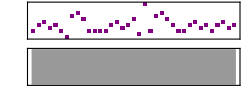

```mathematica
samplemusic=musictemplate[charset];
Sound[samplemusic]
smusicnote=samplemusic[[All,1]];
```

## Several Ways to Split the music

### Simple String Match

#### Brute Force

```mathematica
TransformFromMidi["E:\\MyWorkShop\\midi\\music\\Flower_Dance_主音.mid"];
```

```mathematica
FindMelody[Instrum_]:=(
ssmfull=GetMusicByInstrument[Instrum];
ssmmusic=#[[All,1]]&/@ssmfull;
musiclen=Length[ssmmusic];
minmelodylen=3;
record={};
Do[
Do[
end=start+length-1;
currentsequence=ssmmusic[[start;;end]];
cumusic=ssmfull[[start;;end]];
If[Cases[currentsequence,None]≠{},Continue[],None];
sp=findSubsequence[ssmmusic,currentsequence];
If[Length[sp]>1,
stime=cumusic[[1,1,2,1]];
cumusic[[All,All,2]]-=stime;
record=record~Join~{cumusic};
(ssmmusic[[#;;#+length-1]]=None)&/@sp;
(ssmfull[[#;;#+length-1]]=None)&/@sp;
Break[]
,
None
],{start,1,musiclen-length+1}],
{length,musiclen,minmelodylen,-1}
];
Return[Sound[Flatten@#]&/@record];
)
```

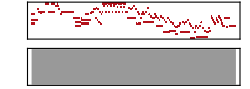
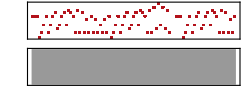
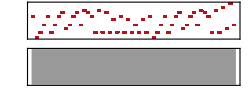
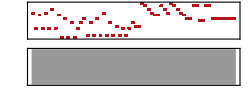
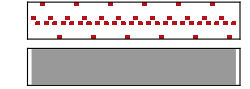
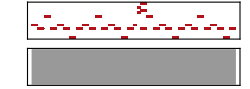
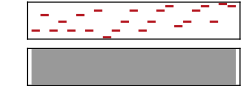
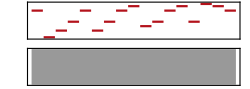

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

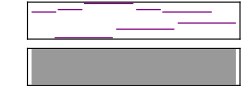
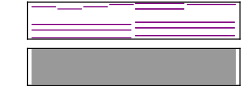
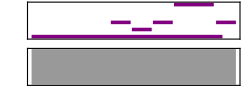
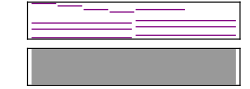
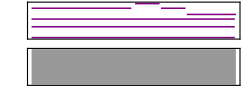
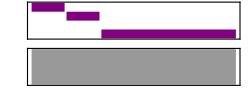

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

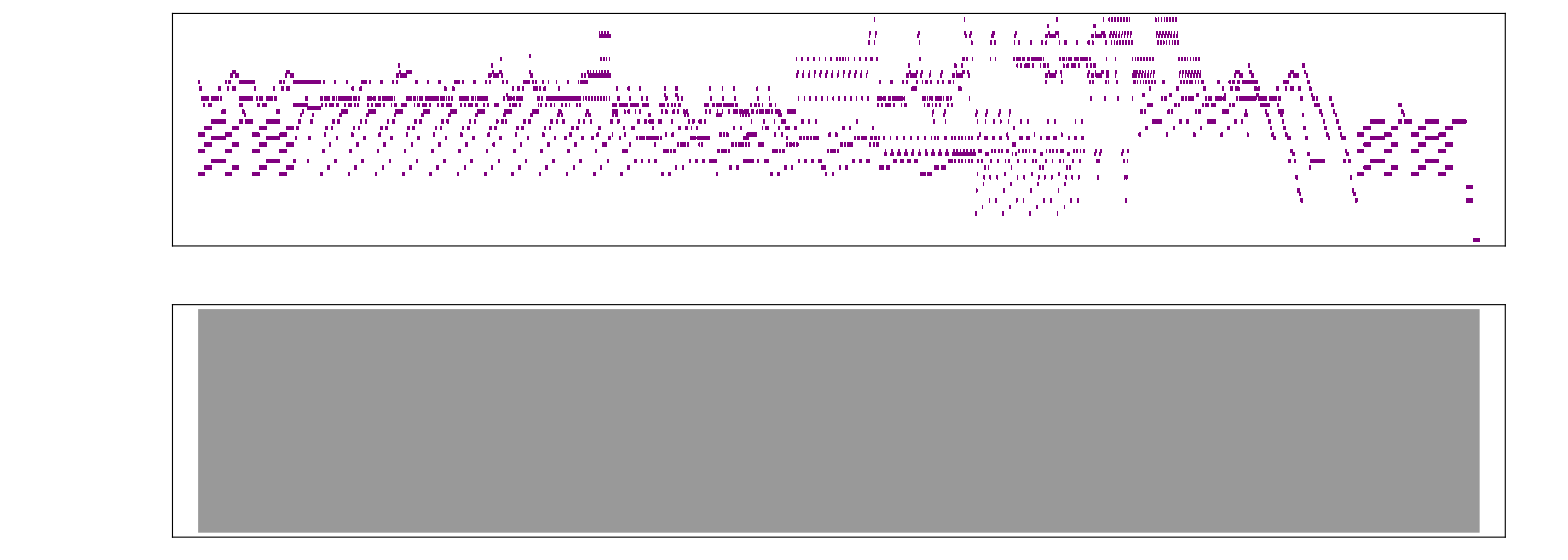

```mathematica
Music[[1]]
```

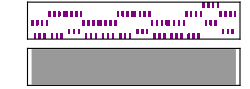
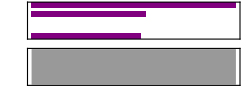
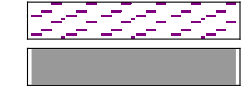
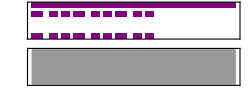
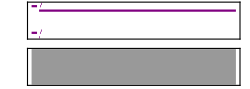
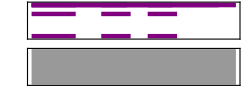
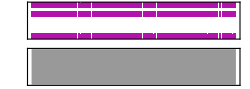
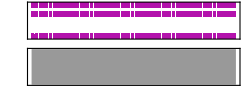

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

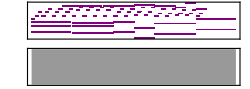
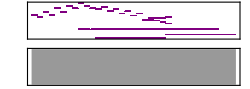
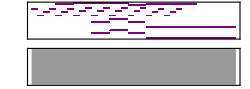
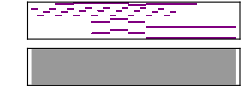
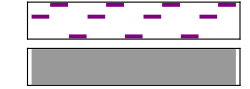
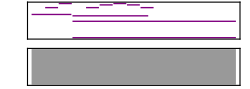
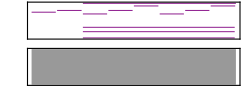
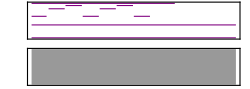

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

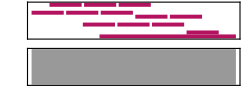
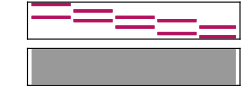
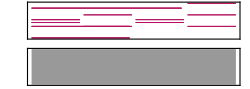
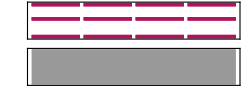
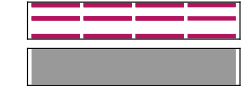
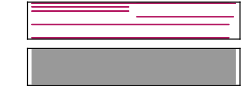
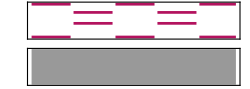
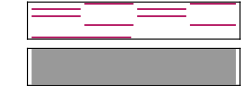

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

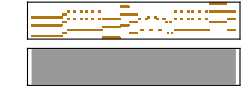
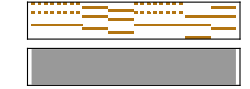
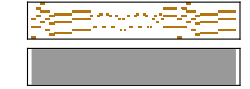
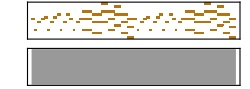
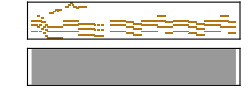
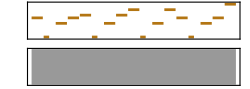
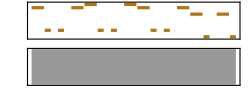
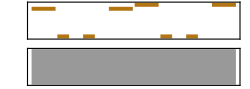
{-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics--Graphics-,,,,,,,,,,,,,}

```mathematica
Row@FindMelody[#]&/@InstrumentList
```

```mathematica
Sound[Flatten@#]&/@record
```

{}

#### Use Aho-Corasick Automaton

```mathematica
Sound[musictemplate[#]]&/@record
```